## Método de Euler

```mathematica
Euler[a0_,b0_,y0_,n0_]:=Module[{a=a0,b=b0,n=n0,i},h=(b-a)/n;T=Table[a+(i-1)h,{i,1,n+1}];Y=Table[y0,{i,1,n+1}];For[i=1,i≤ n,i++,Y_[[i+1]]=Y_[[i]]+h *f[T_[[i]],Y_[[i]]];];
Return[Transpose[{T,Y}]];
]
```

## Ejemplo: y’=1-ty y(0)=1, 0 ≤ t≤ 5

```mathematica
DSolve[{y'[t]== 1-t y[t],y[0]== 1},y[t],t]
```

{{y[t]→1/2 ⅇ^(-t^2/2) (2+√(2 π) Erfi[t/(√2)])}}

```mathematica
fAnalitica[t_]:=1/2 ⅇ^(-t^2/2) (2+√(2 π) Erfi[t/(√2)]);
```

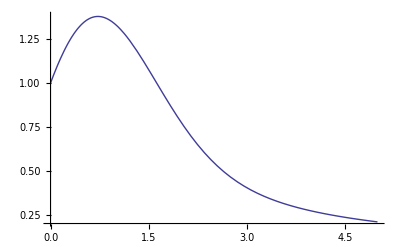

```mathematica
Plot[fAnalitica[t],{t,0,5}]
```

```mathematica
f[t_,y_]:=1-t*y;
```

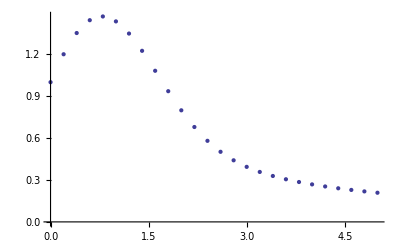

```mathematica
Euler[0.0,5.0,1,25]//ListPlot
```

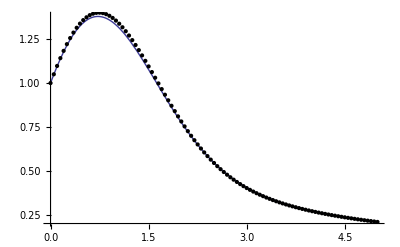

```mathematica
Plot[fAnalitica[t],{t,0,5},Epilog->Map[Point,Euler[0.0,5.0,1,100]]]
```

```mathematica
EulerMejorada[a0_,b0_,y0_,n0_]:=Module[{a=a0,b=b0,n=n0,i},h=(b-a)/n;T=Table[a+(i-1)h,{i,1,n+1}];Y=Table[y0,{i,1,n+1}];For[i=1,i≤ n,i++,Y_[[i+1]]=Y_[[i]]+h *f[T_[[i]]+h/2,Y_[[i]]+h/2*f[T_[[i]],Y_[[i]]]];];
Return[Transpose[{T,Y}]];
]
```

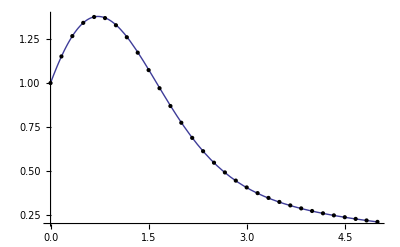

```mathematica
Plot[fAnalitica[t],{t,0,5},Epilog->Map[Point,EulerMejorada[0.0,5.0,1,30]]]
```

## Ejemplo: y'=t^2+y^2 y(0)=1, 0 ≤ t≤ 1

```mathematica
DSolve[{y'[t]== t^2+(y[t])^2,y[0]== 1},y[t],t]
```

{{y[t]→(-t^2 BesselJ[-3/4,t^2/2] Gamma[1/4]+t^2 BesselJ[-5/4,t^2/2] Gamma[3/4]+BesselJ[-1/4,t^2/2] Gamma[3/4]-t^2 BesselJ[3/4,t^2/2] Gamma[3/4])/(t (BesselJ[1/4,t^2/2] Gamma[1/4]-2 BesselJ[-1/4,t^2/2] Gamma[3/4]))}}

```mathematica
gAnalitica[t_]:=(-t^2 BesselJ[-3/4,t^2/2] Gamma[1/4]+t^2 BesselJ[-5/4,t^2/2] Gamma[3/4]+BesselJ[-1/4,t^2/2] Gamma[3/4]-t^2 BesselJ[3/4,t^2/2] Gamma[3/4])/(t (BesselJ[1/4,t^2/2] Gamma[1/4]-2 BesselJ[-1/4,t^2/2] Gamma[3/4]));
```

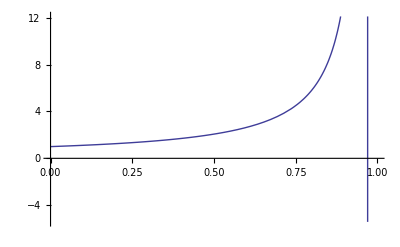

```mathematica
Plot[gAnalitica[t],{t,0,1}]
```

```mathematica
f[t_,y_]:=t^2+y^2;
```

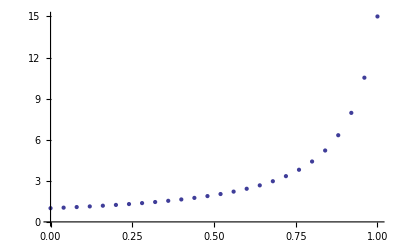

```mathematica
Euler[0.0,1.0,1,25]//ListPlot
```

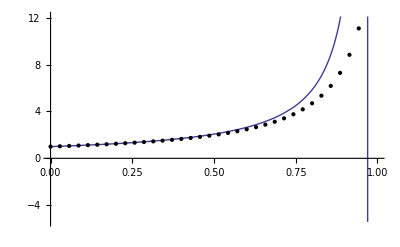

```mathematica
Plot[gAnalitica[t],{t,0,1},Epilog->Map[Point,Euler[0.0,1.0,1,35]]]
```

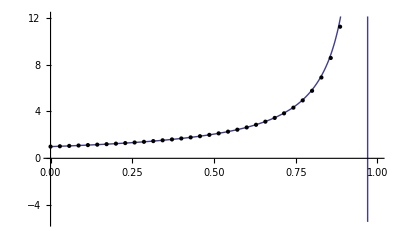

```mathematica
Plot[gAnalitica[t],{t,0,1},Epilog->Map[Point,EulerMejorada[0.0,1.0,1,35]]]
```